# Practical 4

### Submitted By- Puranjytoti Bera (20201043)

Show that the image of the open disk {z:|z+1+i|<1} under the linear transformation w=f(z)=(3-4i)Z+6+2i is the open disk {w:|w+1-3i|<5}

The open disk |z+1+i|<1 is given by the figure

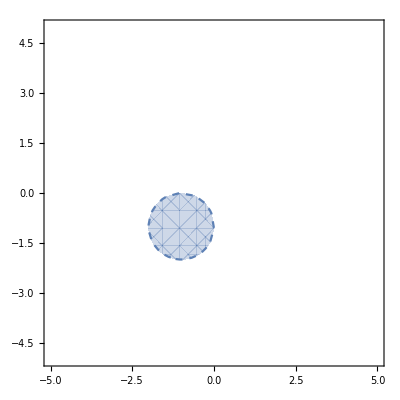

The image of the open disk |z+1+i|<1 under the function f(z)=(6+2 ⅈ)+(3-4 ⅈ) zis1/5 Abs[(1-3 ⅈ)+u+ⅈ v]<1and is given by figure

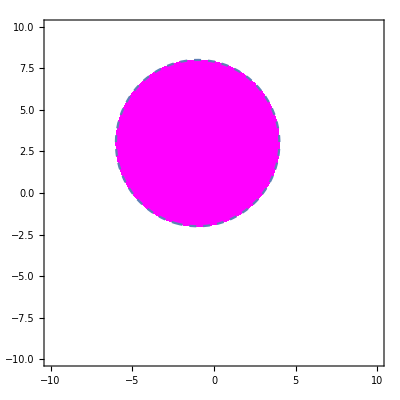

```mathematica
Print["The open disk |z+1+i|<1 is given by the figure"];
RegionPlot[Abs[x+I*y+1+I]<1,{x,-10,10},{y,-10,10},BoundaryStyle->Dashed,PlotRange->5,Axes->True]
f[z_]:=(3-4*I)*z+6+2*I;
w=u+I*v;
root:=z/.ComplexExpand[Solve[f[z]==w,z]];
Print["The image of the open disk |z+1+i|<1 under the function f(z)=",f[z],"is",Simplify[Refine[Abs[root[[1]]+1+I]<1,Element[{u,v},Reals]]],"and is given by figure"];
RegionPlot[Abs[root[[1]]+1+I]<1,{u,-10,10},{v,-10,10},PlotStyle->Magenta,BoundaryStyle->Dashed,PlotRange->10,Axes->True]
```